```mathematica
Clear[Lx,Ly,A,
sx2d,SX2D,sx2dp,SX2DP,
sy2d,SY2D,sy2dp,SY2DP,
cx2d,CX2D,cx2dp,CX2DP,
cy2d,CY2D,cy2dp,CY2DP,
cons,Cons]
```

```mathematica
Lx=5;
Ly=5;
A=Lx*Ly;
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
sx2d[i_Integer,j_Integer]=0;

Do[Do[{sx2d[j+k Lx,j+1+k Lx]=-I/2,sx2d[j+1+k Lx,j+k Lx]=I/2},{j,1,Lx-1}],{k,0,Ly-1}]

SX2D=Table[sx2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
sx2dp[i_Integer,j_Integer]=0;

Do[{sx2dp[(k+1)Lx,1+k Lx]=-I/2,sx2dp[1+k Lx,(k+1)Lx]=I/2},{k,0,Ly-1}]

SX2DP=Table[sx2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
sy2d[i_Integer,j_Integer]=0;

Do[Do[{sy2d[k Lx+j,(k+1)Lx+j]=-I/2,sy2d[(k+1)Lx+j,k Lx+j]=I/2},{j,1,Lx}],{k,0,Ly-2}]

SY2D=Table[sy2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
sy2dp[i_Integer,j_Integer]=0;

Do[{sy2dp[(Ly-1)Lx+j,j]=-I/2,sy2dp[j,(Ly-1)Lx+j]=I/2},{j,1,Lx}]

SY2DP=Table[sy2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
cx2d[i_Integer,j_Integer]=0;

Do[Do[{cx2d[j+k Lx,j+1+k Lx]=1/2,cx2d[j+1+k Lx,j+k Lx]=1/2},{j,1,Lx-1}],{k,0,Ly-1}]

CX2D=Table[cx2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
cx2dp[i_Integer,j_Integer]=0;

Do[{cx2dp[(1+k)Lx,1+k Lx]=1/2,cx2dp[1+k Lx,(1+k)Lx]=1/2},{k,0,Ly-1}]

CX2DP=Table[cx2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
cy2d[i_Integer,j_Integer]=0;

Do[Do[{cy2d[k Lx+j,(k+1)Lx+j]=1/2,cy2d[(k+1)Lx+j,k Lx+j]=1/2},{j,1,Lx}],{k,0,Ly-2}]

CY2D=Table[cy2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
cy2dp[i_Integer,j_Integer]=0;

Do[{cy2dp[(Ly-1)Lx+j,j]=1/2,cy2dp[j,(Ly-1)Lx+j]=1/2},{j,1,Lx}]

CY2DP=Table[cy2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*--------------- Lattice model for a constant matrix ---------------*)
```

```mathematica
cons[i_Integer, j_Integer]:=0

Do[{cons[i,i]=1},{i,1,A}]

Cons=Table[cons[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[σ0,σ1,σ2,σ3,HamiltonianQAHI]
```

```mathematica
σ0=PauliMatrix[0];
σ1=PauliMatrix[1];
σ2=PauliMatrix[2];
σ3=PauliMatrix[3];
```

```mathematica
HamiltonianQAHI[t_,t0_,m_,α_]:=t*(KroneckerProduct[σ1,SX2D+α*SX2DP]+KroneckerProduct[σ2,SY2D+α*SY2DP])+KroneckerProduct[σ3,m*Cons+t0*(CX2D+CY2D+α*CX2DP+α*CY2DP)]
```

```mathematica
(*--------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[val,vec,ValVecAHI,ValAHI,ValAHIRange]
```

```mathematica
{val,vec}=Eigensystem[HamiltonianQAHI[1.0,1.0,-1.0,0.0]];
```

```mathematica
ValVecAHI=SortBy[Transpose[{val,vec}],First];
```

```mathematica
ValAHI=Table[{j,Re[ValVecAHI[[j,1]]]},{j,1,2A}];
```

```mathematica
ValAHIRange=Table[ValAHI[[j,2]],{j,1,2 A}];
```

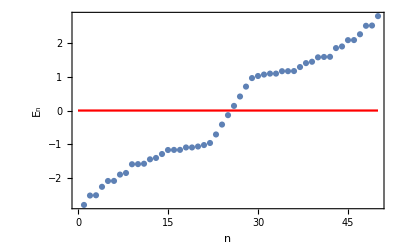

```mathematica
Show[ListPlot[ValAHI,Frame-> True,Axes-> False,PlotRange-> {{0,2A},{Min[ValAHIRange],Max[ValAHIRange]}}],Plot[0,{x,0,2A},PlotStyle-> Red],BaseStyle-> 14,FrameStyle-> Black,FrameLabel-> {"n","E_n"}]
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[Sitelocation,FlatSite,Sites, LineUp,LineDn]
```

```mathematica
Sitelocation=Table[{i,j},{i,1,Lx},{j,1,Ly}];
```

```mathematica
FlatSite=Flatten[Sitelocation];
```

```mathematica
NOrbitals=Dimensions[FlatSite][[1]]
```

50

```mathematica
Sites=Table[{FlatSite[[i]],FlatSite[[i+1]]},{i,1,NOrbitals,2}];
```

```mathematica
(**--Equations for the two red lines--**)
```

```mathematica
LineUp[x_]:=((1+√5)/2)^-1*(x-1)+2
LineDn[x_]:=((1+√5)/2)^-1*(x-2)+1
```

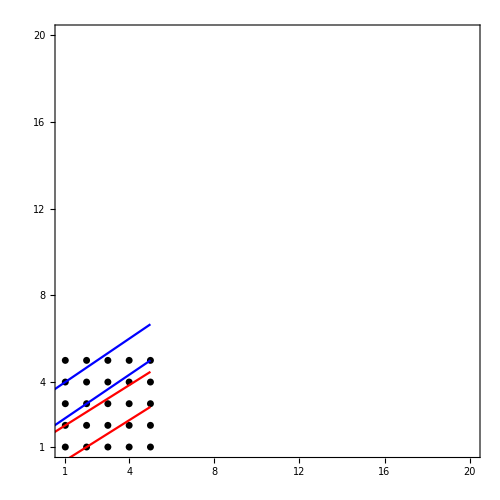

```mathematica
Show[ListPlot[Sites,PlotStyle-> {Black,PointSize[0.01]},Frame-> True,Axes-> False,PlotRange-> {{0.9,20.1},{0.9,20.1}}],
Plot[2/3*(x-1)+4,{x,0,Lx},PlotStyle-> Blue],Plot[2/3*(x-2)+3,{x,0,Lx},PlotStyle-> Blue],
Plot[((1+√5)/2)^-1*(x-1)+2,{x,0,Lx},PlotStyle-> Red],
Plot[((1+√5)/2)^-1*(x-2)+1,{x,0,Lx},PlotStyle-> Red],
FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},BaseStyle-> 16,
FrameTicks-> {{{{1,"1"},{4,"4"},{8,"8"},{12,"12"},{16,"16"},{20,"20"}},None},{{{1,"1"},{4,"4"},{8,"8"},{12,"12"},{16,"16"},{20,"20"}},None}},
ImageSize-> 500,AspectRatio-> 1
]
```

```mathematica
(*-----------------------------------------------------------------------------*)
```

```mathematica
Clear[Fibonup,Fibondown,TotalFibon]
```

```mathematica
(**-----We want to count points inside the area of interest, store them in FibonupNew, and sort them into Fibonup-----**)
```

```mathematica
Clear[FibonupNew]
FibonupNew={};
```

```mathematica
(**---Points on the lines are not taken---**)
```

```mathematica
(**---That is why we calculate Floor[]+1 instead of Ceiling, and Ceiling[]-1 instead of Floor---**)
```

```mathematica
Do[Do[FibonupNew=Append[FibonupNew,x+(y-1)*Ly],{y,Max[1,Floor[LineDn[x]]+1],Min[Ly,Ceiling[LineUp[x]]-1]}],{x,1,Lx}]
```

```mathematica
Fibonup=Sort[FibonupNew]
```

{1,7,8,13,14,15,20}

```mathematica
YList = Ceiling[Fibonup/Lx];
```

```mathematica
XList = Fibonup - (YList - 1)Lx;
```

```mathematica
(**Check**)
```

```mathematica
XList + (YList-1)*Lx - Fibonup
```

{0,0,0,0,0,0,0}

```mathematica
XListKron = Flatten[KroneckerProduct[XList,{1,1}],2];
```

```mathematica
YListKron = Flatten[KroneckerProduct[YList,{1,1}],2];
```

```mathematica
Ux =DiagonalMatrix[ Exp[2 π I XListKron /Lx]];
```

```mathematica
Vy = DiagonalMatrix[Exp[2 π I YListKron/Ly]];
```

```mathematica
(**--Compare with the previous (manually calculated) Fibonup for 20x20 sites--**)
```

```mathematica
(**--Fibonup={1,22,23,43,44,45,65,66,86,87,88,108,109,110,130,131,151,152,153,173,174,194,195,196,216,217,218,238,239,259,260};--**)
```

```mathematica
Fibondown=Table[Fibonup[[j]]+A,{j,1,Dimensions[Fibonup][[1]]}];
```

```mathematica
TotalFibon=Flatten[{Fibonup,Fibondown}];
```

```mathematica
NOrbitalsQuasi=Dimensions[TotalFibon][[1]]
```

14

```mathematica
NOrbitalsOutside = NOrbitals-NOrbitalsQuasi
```

36

```mathematica
(*-----------------------------------------------------------------------------*)
```

```mathematica
Clear[F1,a]
```

```mathematica
F1=Table[i,{i,1,2*A}];
```

```mathematica
a=F1;
Do[
a=Drop[a,{TotalFibon[[NOrbitalsQuasi-i]]}],
{i,0,NOrbitalsQuasi-1,1}
]
```

```mathematica
Dimensions[a]
```

{36}

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[HTrial,Hfbfb,HFBFB,H2d2d,H2D2D,H2dfb,H2DFB,Hfb2d,HFB2D]
```

```mathematica
HTrial=KroneckerProduct[σ1,CX2D];
```

```mathematica
(*---------------------------------------------------------*)
```

```mathematica
Hfbfb[i_Integer,j_Integer]=0;
Do[
Do[
Hfbfb[i,j]=HTrial[[TotalFibon[[i]],TotalFibon[[j]]]],
{i,1,NOrbitalsQuasi}
],
{j,1,NOrbitalsQuasi}
]
HFBFB=Table[Hfbfb[i,j],{i,1,NOrbitalsQuasi},{j,1,NOrbitalsQuasi}];
```

```mathematica
(*---------------------------------------------------------*)
```

```mathematica
H2d2d[i_Integer,j_Integer]=0;
Do[
Do[
H2d2d[i,j]=HTrial[[a[[i]],a[[j]]]],
{i,1,NOrbitalsOutside}
],
{j,1,NOrbitalsOutside}
]
H2D2D=Table[H2d2d[i,j],{i,1,NOrbitalsOutside},{j,1,NOrbitalsOutside}];
```

```mathematica
(*------------------------------------------------------*)
```

```mathematica
H2dfb[i_Integer,j_Integer]=0;

Do[
Do[
H2dfb[i,j]=HTrial[[a[[i]],TotalFibon[[j]]]],
{i,1,NOrbitalsOutside}
],
{j,1,NOrbitalsQuasi}
]
H2DFB=Table[H2dfb[i,j],{i,1,NOrbitalsOutside},{j,1,NOrbitalsQuasi}];
```

```mathematica
(*-------------------------------------------------*)
```

```mathematica
Hfb2d[i_Integer,j_Integer]=0;

Do[
Do[
Hfb2d[i,j]=HTrial[[TotalFibon[[i]],a[[j]]]],
{i,1,NOrbitalsQuasi}
],
{j,1,NOrbitalsOutside}
]
HFB2D=Table[Hfb2d[i,j],{i,1,NOrbitalsQuasi},{j,1,NOrbitalsOutside}];
```

```mathematica
(*---------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[HFibonRenor,ValueFibon,VecFibon,ValVecFibon,ValFibon,OnlyEigenvalue]
```

```mathematica
Inverse[SX2D];
```

Inverse::sing: Matrix {{0,-ⅈ/2,0,0,0,0,0,0,0,0,«15»},{ⅈ/2,0,-ⅈ/2,0,0,0,0,0,0,0,«15»},{0,ⅈ/2,0,-ⅈ/2,0,0,0,0,0,0,«15»},{0,0,ⅈ/2,0,-ⅈ/2,0,0,0,0,0,«15»},{0,0,0,ⅈ/2,0,0,0,0,0,0,«15»},{0,0,0,0,0,0,-ⅈ/2,0,0,0,«15»},{0,0,0,0,0,ⅈ/2,0,-ⅈ/2,0,0,«15»},{0,0,0,0,0,0,ⅈ/2,0,-ⅈ/2,0,«15»},{0,0,0,0,0,0,0,ⅈ/2,0,-ⅈ/2,«15»},{0,0,0,0,0,0,0,0,ⅈ/2,0,«15»},«15»} is singular.

```mathematica
Inverse[H2D2D];
```

Inverse::sing: Matrix {{0,0,0,0,0,0,0,0,0,0,«26»},{0,0,0,0,0,0,0,0,0,0,«26»},{0,0,0,0,0,0,0,0,0,0,«26»},{0,0,0,0,0,0,0,0,0,0,«26»},{0,0,0,0,0,0,0,0,0,0,«26»},{0,0,0,0,0,0,0,0,0,0,«26»},{0,0,0,0,0,0,0,0,0,0,«26»},{0,0,0,0,0,0,0,0,0,0,«26»},{0,0,0,0,0,0,0,0,0,0,«26»},{0,0,0,0,0,0,0,0,0,0,«26»},«26»} is singular.

```mathematica
(*HFibonRenor=HFBFB-(HFB2D.Inverse[H2D2D].H2DFB);*)
```

```mathematica
(*HFibonRenor*)
```

```mathematica
(**------HFibonRenor is Hermitian------**)
```

```mathematica
(*ConjugateTranspose[HFibonRenor] - HFibonRenor//Chop;*)
```

```mathematica
(*ArrayPlot[Im[HFibonRenor[[1;;NOrbitalsQuasi,1;;NOrbitalsQuasi]]],Frame-> True,Axes-> False,FrameStyle-> {Black,Thick},ColorFunction->"DarkRainbow"]*)
```